# Problem set 4

## 1. First box-counting

The first one has λ that i equal to 1/3. There are 9(3^2) boxes needed to calculate the first one 4(2^2) boxes are needed.
In the second one we need 9*9 boxes(3^4) each with an area of 3^-4 and 16(2^4) boxes are filled. The formula for these are

```mathematica
N[Limit[Log[2^(2*n)]/Log[3^(2*n)],n-> Infinity]]
```

0.63093

## Second box-counting

In the second exercise we have that the smallest box as a side of 1/4. These boxes have an area of (1/4)^2 = 1/(16)=2^(-4).  The first relative area length λ_1 is 2^(-4). λ_2 has an area of (1/2)^2=2^(-2).
From lecture 12 we have an expression for the dimension

We have 4 boxes we area 1/16=2^-4 and one with area 1/4 wich is the same as 4 more boxes with area 1/16. The total number of boxes is 8=2^3

In the second we have that the smallest box has an area of 1 /256=2^-8. There are a 16 om these boxes
Each box with a side of 1/8, contains 4 of these boxes. There are a total of 8 boxes with sides 1/8, which gives us 4*8= 32 boxes
The box in the middle has an area of 1/16=2^(-4), which is 2^-4/2^-8 =2^4=16 boxes
The total number of boxes are then 16+32+16=64 boxes=2^6

ϵ is in this task equal to 4^n(=2^(2*n)) and the number of boxes are equal to 2^(3*n). The dimesion

```mathematica
Limit[Log[2^(2*n)]/Log[2^(3*n)],n-> Infinity]
```

2/3

## Plot the approximation of the Hénon map

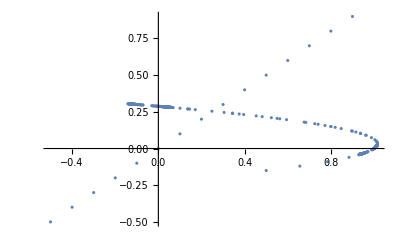

```mathematica
data={};

For[j=-0.5,j<1,j=j+1/10,
       x=j;
y=j;
AppendTo[data,{x,y}];
For[i=0,i<100,i++,
y=0.3*x;
x=y+1-1.4*x^2;

AppendTo[data,{x,y}];
]
]
ListPlot[data]
```